## Techniques Final

### 2

#### b

```mathematica
Quantity[, "PlanckConstant"]*Quantity[, "SpeedOfLight"]/Quantity[1.12, "Electronvolts"]//UnitConvert
```

1.107×10^-6 m

#### d

Total shifts: 2048 parallel shifts down, and 2048^2 serial shifts out.  
Total cycles: #shifts*3
Total time: #cycles/rate

```mathematica
(2048+2048^2)shifts*3 cycles/shifts/(10^7 cycles/Quantity[, "Seconds"])//N
```

1.25891 s

#### e

CTE is % of electrons successfully moved during one pixel shift
How many times is the last pixel moved?  It’s moved 2048 times parallel and 2048 times serially.
And fraction=CTE^(2048+2048)

```mathematica
(.999)^(2*2048)
```

0.016605

```mathematica
ScientificForm[0.016605034169726227]
```

1.6605×10^-2

### 4

```mathematica
SNR[n_, npix_,b_,d_,ρ_,t_]:=n *t/√(n*t+2npix(b*t+d*t+ρ))
```

#### a

```mathematica
SNR[45 /Quantity[, "Seconds"],9p ,1.4/Quantity[, "Seconds"] /p, 2 /Quantity[, "Seconds"]/p,4 /p,t Quantity[, "Seconds"]]//FullSimplify
```

(45 t)/(√(72.+106.2 t))

Read noise dominates

#### b

```mathematica
SNR[45 /Quantity[, "Seconds"],25p ,1.4/Quantity[, "Seconds"] /p, 4 /Quantity[, "Seconds"]/p,4 /p,25 Quantity[, "Seconds"]]//FullSimplify
```

12.5193

moon brightness dominates

### 5

#### b

gain=(#e/pix)/(#counts/pix)

```mathematica
45e/Quantity[, "Seconds"]*25 Quantity[, "Seconds"]/(5 e/ADU)
```

225 ADU

```mathematica
225 ADU/9
```

25 ADU

#### c

```mathematica
√(45e/Quantity[, "Seconds"]*25 Quantity[, "Seconds"]/(5 e/ADU))
```

15 √ADU

### 6

```mathematica
data={{1.2,8.56},{1.5,8.57}}
```

{{1.2,8.56},{1.5,8.57}}

```mathematica
m=LinearModelFit[data,X,X]
```

FittedModel[8.52+0.0333333 X]

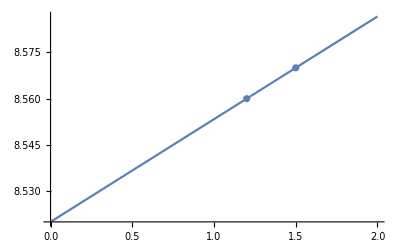

```mathematica
Show[Plot[m[X],{X,0,2}],ListPlot[data]]
```

#### a

```mathematica
k=m["BestFitParameters"][[2]]
```

0.0333333

```mathematica
mi=m[0]
```

8.52

#### b

```mathematica
Δm=.4
```

0.4

```mathematica
Cstd=.3
```

0.3

```mathematica
Δm==ζ+ϵ Cstd
```

0.4==0.3 ϵ+ζ

### 7

#### a

```mathematica
Quantity[20, "Micrometers"]*Quantity[25, ("Nanometers")/("Millimeters")]
```

1/2 nm

#### b

```mathematica
Quantity[550, "Nanometers"]/Quantity[1/2, "Nanometers"]
```

1100

#### c

```mathematica
Quantity[700, "Nanometers"]/(10+1)
```

700/11 nm

#### d

```mathematica
Solve[(656-410+533+x)/64==12]
```

{{x→-11}}

```mathematica
533-11
```

522

12.1719

### 8

```mathematica
i[s_,q_,μ_,η_,τ_,V_,n_]:=s^-2 q μ η τ V n
```

#### a

```mathematica
i[Quantity[10, "Nanometers"],1 Entity["Particle","Electron"][EntityProperty["Particle","Charge"]],Quantity[1/10^4, ("Meters")^2/("Seconds" "Volts")], .8,Quantity[1/10^6, "Seconds"],Quantity[10, "Volts"],100/Quantity[, "Seconds"]]//FullSimplify
```

-8.×10^8 e/s

#### b

η is incident/total=0.8.  And 90% of incident photons make it to the detector.  So 90% of incident photons make it to detector, but only 80% of photons that hit the detector are counted.  So .9 *a=.8

```mathematica
a=a/.Solve[.9*a==.8][[1]]
```

0.888889

Therefore 89% must be either transmitted or absorbed

#### c

```mathematica
Solve[a==ⅇ^(-10^4 1/Quantity[, "Meters"]z),z]//ScientificForm
```

{{z→1.17783×10^-5 m}}

### 9

```mathematica
d[T_,Eg_]:=4.3*10^10 T^(3/2)ⅇ^(-Eg/(2 Quantity[, "BoltzmannConstant"]T))
```

#### a

```mathematica
d[Quantity[300, "Kelvins"],1.12 Quantity[, "Electronvolts"]]
```

87410.7 K^(3/2)

#### b

```mathematica
d[Quantity[233, "Kelvins"],1.12 Quantity[, "Electronvolts"]]
```

117.959 K^(3/2)

### 10

#### a

```mathematica
2^16-1
```

65535

There’s 65,535 values and a maximum well capacity of 300,000.  So for each electron, you probably want to have

```mathematica
300000/(2^16-1)//N
```

4.57771

counts.

#### b

```mathematica
100000/(2^8-1)//N
```

392.157